```mathematica
(*Setup variables*)
n = RandomInteger[{3,6}];
poly = RandomPolygon[{"Convex",n}];
boundary = RegionBoundary[poly];
sides = Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ boundary));
centroid = RegionCentroid[poly];
ray = HalfLine[centroid,5*AngleVector[RandomReal[{0,2*Pi}]]];
breakPoint = RandomPoint @ boundary;
initialDirection = breakPoint - centroid;
```

```mathematica
sideList[poly_] := Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ RegionBoundary[poly]));
```

```mathematica
getCurrentSide[poly_,point_] := Extract[#,{1}]& @ First @ SortBy[RegionDistance[#,point]&] @ sideList[poly];
```

```mathematica
lineToVecRep[line_] := (
line[[2]]-line[[1]]
);
```

```mathematica
(*Calculates raycast from an arbitrary starting point and angle in a polygon*)
castRayPolygon[poly_, point_,originVector_] := Module[{currentSide,ray,sides,collisions,pointOfCollision,oppRay,newDirection,possibleCollisions},
sides = sideList[poly];
currentSide = getCurrentSide[poly,point];
newDirection = calculateNewDirection[originVector,lineToVecRep[currentSide]];
ray = HalfLine[point,newDirection];
possibleCollisions =   (List @@ RegionIntersection[ray,RegionBoundary@ poly])[[1]];
pointOfCollision = Last @ (SortBy[EuclideanDistance[#,point]&][possibleCollisions]);
collisionSide = Extract[#,{1}]& @ Last @ SortBy[sides, RegionDistance[#,pointOfCollision]&];
Return @ {pointOfCollision, currentSide,point,newDirection};
];
```

```mathematica
castRayPolygonNestable[poly_, {point_,originVector_}] := (
	castRayPolygon[poly,point,originVector][[{1,4}]]
);
```

This function calculates the new direction vector of the ball based on the incoming direction and the side that it hit.

```mathematica
calculateNewDirection[originVector_, sideVec_]:= (
Normalize[(2*Projection[originVector,sideVec]-originVector)]
);
```

```mathematica
rays = {};
AppendTo[rays, Line[{breakPoint,centroid}]];
```

```mathematica
castInfo = castRayPolygon[poly, breakPoint, breakPoint-centroid];
AppendTo[rays,Line[{castInfo[[3]],castInfo[[1]]}]];
```

```mathematica
casts = Reap @ Nest[Sow[castRayPolygonNestable[poly,#]]&,{breakPoint,breakPoint-centroid},1000000];
AppendTo[rays, Line /@ Partition[(Transpose @ casts[[2]][[1]] )[[1]],2,1]];
```

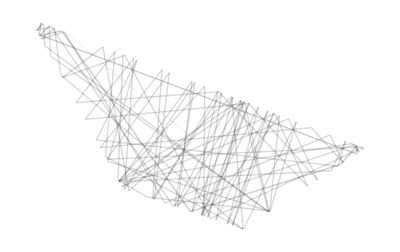

```mathematica
Graphics[{Opacity[0.05],rays}]
```